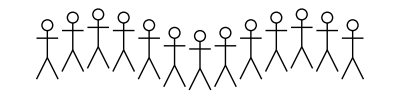

```mathematica
drawPerson[{x_, y_}] := {Black, Line[{{x, y}, {x+1, y+2}, {x+2, y}}], Line[{{x+1, y+2}, {x+1, y+4.5}}],Line[{{x,y+3.8},{x+2,y+3.8}}], Circle[{x+1, y+4.5+.5}, .5]}

Graphics[Table[drawPerson[{x*3,Sin[x]}],{x, 0, 3*Pi, Pi/4}]]
```